# Code

## Mathematical Model of a Personalized Neoantigen Cancer Vaccine and the Human Immune System

Author: Marisabel Rodriguez Messan, PhD

U.S. Food and Drug Administration, Silver Spring, MD 20993

This code solves a non-linear system of ODE’s with scheduled constant vaccine doses. 
The code is designed to use patient-specific information such as HLA affinities, peptide-vaccine concentration,and  initial tumor cell count (or size).
The output simulations show the total number of activated T-cells and  tumor cell count throughout treatment.

To run this code (Shift+Enter to execute each cell):
1. Initialize
2. Import data (Patients_HLA_BA.xlsx, TcellscountsNEW.xlsx, and Best-Fits.xlsx)
3. Estimate patients’ tumor size 
4. Now you can solve the ODE system

## Initialization

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Marisabel.Rodriguez\OneDrive - FDA\CancerVax\SUBMISSION\Code

Settings for nice plot legends

```mathematica
legendoptions={LabelStyle->{Bold,Black,16},LegendMarkerSize->{25,30}};
```

## Importing Data

Melanoma patients (6 total)

```mathematica
dataNetMHCIIpanAll=Import["Patients_HLA_BA.xlsx",{"XLSX","Data",2},"HeaderLines"->1];
dataNetMHCIpanAll=Import["Patients_HLA_BA.xlsx",{"XLSX","Data",1},"HeaderLines"->1];
TcellsPatientData = Import["TcellscountsNEW.xlsx",{"XLSX","Data",1},"HeaderLines"-> 1];
ParmEstim=Import["Best-Fits.xlsx",{"XLSX","Data",1},"HeaderLines"->1];
```

### Cleaning and organizing patient data

#### Melanoma patients

If imported as “Data”, Grid lets you visualize as a table

```mathematica
Grid[TcellsPatientData];
```

Choose all rows and columns 1, 2, 8, 9

```mathematica
FullDose = TcellsPatientData[[All,{1,2,8,9}]];
```

Multiply 3rd column by 1.42857 x10^6

```mathematica
FullDoseScaleUp= FullDose/.{x_,y_,z_,w_}->{x,y,(1.42857*^6)*z,w}; (*Spot-forming cells per 10^6; there are ~1.42857x10^12 PBMCs*)
```

Group by Patients; select a specific patient

```mathematica
byPatient = GatherBy[FullDoseScaleUp,#[[2]]&];
```

```mathematica
patient1 = Select[FullDoseScaleUp,#[[2]]==1&];
patient2 = Select[FullDoseScaleUp,#[[2]]==2&];
patient3 = Select[FullDoseScaleUp,#[[2]]==3&];
patient4 = Select[FullDoseScaleUp,#[[2]]==4&];
patient5 = Select[FullDoseScaleUp,#[[2]]==5&];
patient6 = Select[FullDoseScaleUp,#[[2]]==6&];
```

## Initial tumor size estimation

Cell count (volume of a sphere, minus void volume, times 100,000)

```mathematica
Vc[d_]:=((4 Pi)/3*(d/2)^3)(0.7405)(1*^5)
```

Estimation of diameter size given cell count. Input number of cells; Output diameter in millimeters

```mathematica
Diam[cells_]:=Solve[((4 Pi)/3*(d/2)^3)(0.7405)(1*^5)==cells,d,Reals]
```

```mathematica
Diam[3.3*^8]
```

{{d→20.4172}}

```mathematica
tumorFun =Flatten[Table[NDSolve[{T'[τ]==0.004(1-T[τ]/(1.45*^10))T[τ],T[0]==t0},{T},{τ,0,180}],{t0,{851056,7.27*^8,608728,726984,500165,7.27*^8}}]];
```

```mathematica
Grid[{{Text[Style["Patient",Bold]],Text[Style["Stage by tumor\ntickness",Bold]],Text[Style["Tumor cell count\nBEFORE sugery",Bold]],Text[Style["Tumor cell count\nAFTER sugery (5%)",Bold]],Text[Style["Time lag (days)",Bold]],Text[Style["Tumor cell count\nat the beginning\nof treatment",Bold]]},
{1,Text["T3 (N3M0)"],Vc[4]+3*Vc[5],(Vc[4]+3*Vc[5])*.05,120,T[τ]/.tumorFun[[1]]/.τ->120},
{2,Text["T4 (N0M1b)"],Vc[5]+3*Vc[50],(Vc[5]+3*Vc[50])*.05,120,T[τ]/.tumorFun[[2]]/.τ->120},
{3,Text["T3 (N2M0)"],Vc[4]+2*Vc[5],(Vc[4]+2*Vc[5])*.05,165,T[τ]/.tumorFun[[3]]/.τ->165},
{4,Text["T4 (N2M0)"],Vc[5]+2*Vc[5],(Vc[5]+2*Vc[5])*.05,180,T[τ]/.tumorFun[[4]]/.τ->180},
{5,Text["T2 (N2M0)"],Vc[2]+2*Vc[5],(Vc[2]+2*Vc[5])*.05,135,T[τ]/.tumorFun[[5]]/.τ->135},
{6,Text["T2 (N0M1b)"],Vc[2]+3*Vc[50],(Vc[2]+3*Vc[50])*.05,105,T[τ]/.tumorFun[[6]]/.τ->105}},Frame->All,Background->{None,{LightBlue}},Spacings->{Automatic,.8},ItemStyle->Directive[FontSize->14],Alignment->{Center,Center}]
```

Patient | Stage by tumor
tickness | Tumor cell count
BEFORE sugery | Tumor cell count
AFTER sugery (5%) | Time lag (days) | Tumor cell count
at the beginning
of treatment
1 | T3 (N3M0) | 1.70211×10^7 | 851056. | 120 | 1.37532×10^6
2 | T4 (N0M1b) | 1.45445×10^10 | 7.27227×10^8 | 120 | 1.13968×10^9
3 | T3 (N2M0) | 1.21746×10^7 | 608728. | 165 | 1.17772×10^6
4 | T4 (N2M0) | 1.45397×10^7 | 726984. | 180 | 1.49346×10^6
5 | T2 (N2M0) | 1.00033×10^7 | 500165. | 135 | 858265.
6 | T2 (N0M1b) | 1.454×10^10 | 7.27×10^8 | 105 | 1.07825×10^9

## Plots of Melanoma Patient Data (T-cell responses)

### Plots by Patient and All Patients

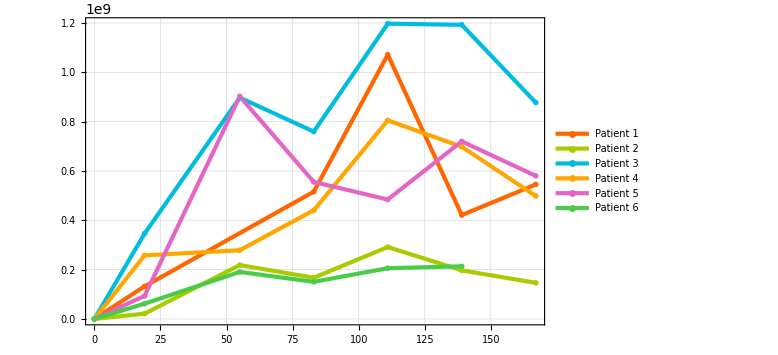

```mathematica
ListLinePlot[#[[All,{1,3}]]&/@byPatient,PlotTheme->{"NeonColor","Detailed","ThickLines"},PlotMarkers->"OpenMarkersThick",LabelStyle->Directive[Black,Bold, 16],FrameStyle->Directive[Black],PlotLegends->Placed[LineLegend[{"Patient 1","Patient 2","Patient 3","Patient 4","Patient 5","Patient 6"},LegendFunction->(Framed[#,RoundingRadius->5]&)],Below],ImageSize->Large]
```

```mathematica
linecolors={ColorData[106][1],ColorData[106][2],ColorData[106][3],ColorData[106][4],ColorData[106][5],ColorData[106][6]};lineWidth={Thickness[0.006],Thickness[0.006],Thickness[0.006],Thickness[0.006],Thickness[0.006],Thickness[0.006]};
```

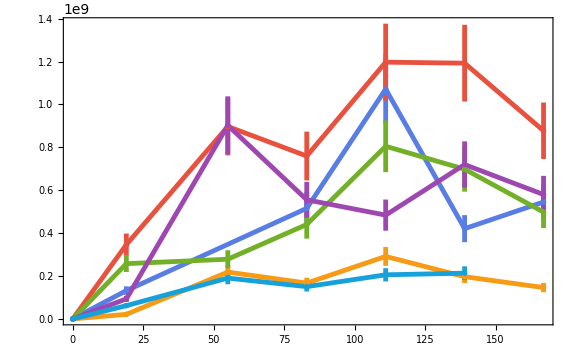

```mathematica
ListLinePlot[Thread[{#[[All,1]],Thread[Around[#[[All,3]],Scaled[0.15]]]}]&/@byPatient,PlotStyle->Transpose[{linecolors,lineWidth}],PlotMarkers->{"OpenMarkersThick",8},LabelStyle->Directive[Black,Bold,20],Frame->True,FrameStyle->Directive[Black,Thick],PlotLegends->Placed[LineLegend[{"Patient 1","Patient 2","Patient 3","Patient 4","Patient 5","Patient 6"},LegendFunction->(Framed[#,RoundingRadius->5]&)],Below],ImageSize->Large]
```

```mathematica
patient1adjusteddata=Thread[{patient1[[All,1]],Thread[Around[patient1[[All,3]],Scaled[0.15]]]}]
```

{{0.,1.430.21},{19.,1.320.2010^8},{83.,5.20.810^8},{111.,1.070.1610^9},{139.,4.20.610^8},{167.,5.50.810^8}}

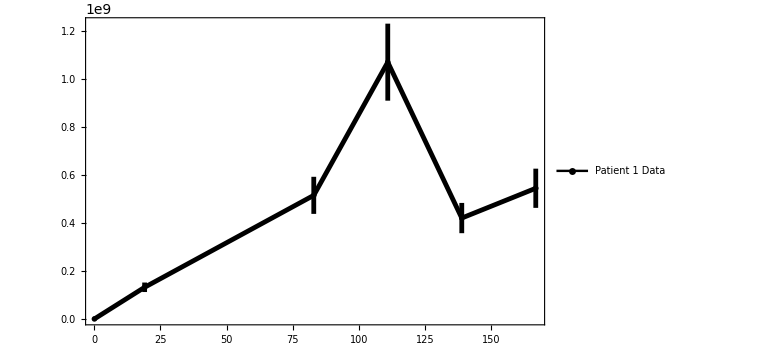

```mathematica
P1Plot=ListLinePlot[patient1adjusteddata,PlotMarkers->{"OpenMarkersThick",8},(*IntervalMarkersStyle->Gray,*)PlotStyle->Directive[Black,Thickness[0.006]],LabelStyle->Directive[Black,Bold, 18],Frame->True,FrameStyle->Directive[Black,Thick],PlotLegends->Placed[LineLegend[{"Patient 1 Data"},legendoptions],{0.2,0.88}],ImageSize->Large]
```

```mathematica
P1Plot=ListLinePlot[patient1adjusteddata,PlotMarkers->{"OpenMarkersThick",8},(*IntervalMarkersStyle->Gray,*)PlotStyle->Directive[Black,Thickness[0.006]],LabelStyle->Directive[Black,Bold, 18],Frame->True,FrameStyle->Directive[Black,Thick],PlotLegends->Placed[LineLegend[{"Patient 1 Data"},legendoptions],{0.2,0.88}],ImageSize->Large]
```

-Graphics-

```mathematica
patient2adjusteddata=Thread[{patient2[[All,1]],Thread[Around[patient2[[All,3]],Scaled[0.15]]]}]
```

{{0.,1.430.21},{19.,2.140.3210^7},{55.,2.180.3310^8},{83.,1.670.2510^8},{111.,2.90.410^8},{139.,1.970.3010^8},{167.,1.460.2210^8}}

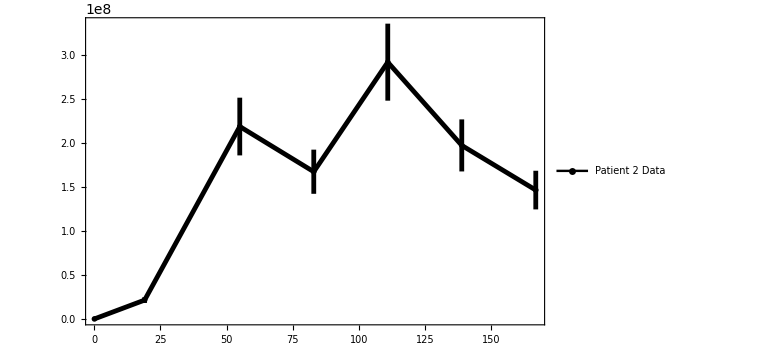

```mathematica
P2Plot=ListLinePlot[patient2adjusteddata,PlotMarkers->{"OpenMarkersThick",8},(*IntervalMarkersStyle->Gray,*)PlotStyle->Directive[Black,Thickness[0.006]],LabelStyle->Directive[Black,Bold, 18],Frame->True,FrameStyle->Directive[Black,Thick],PlotLegends->Placed[LineLegend[{"Patient 2 Data"},legendoptions],{0.2,0.9}],ImageSize->Large]
```

```mathematica
patient3adjusteddata=Thread[{patient3[[All,1]],Thread[Around[patient3[[All,3]],Scaled[0.15]]]}]
```

{{0.,1.430.21},{19.,3.50.510^8},{55.,9.01.310^8},{83.,7.61.110^8},{111.,1.200.1810^9},{139.,1.190.1810^9},{167.,8.81.310^8}}

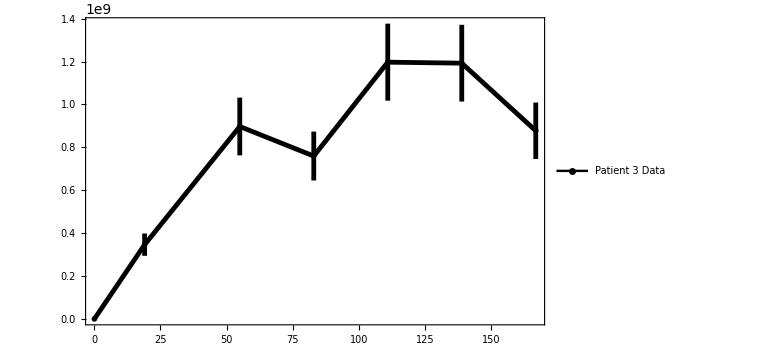

```mathematica
P3Plot=ListLinePlot[patient3adjusteddata,PlotMarkers->{"OpenMarkersThick",8},(*IntervalMarkersStyle->Gray,*)PlotStyle->Directive[Black,Thickness[0.006]],LabelStyle->Directive[Black,Bold, 18],Frame->True,FrameStyle->Directive[Black,Thick],PlotLegends->Placed[LineLegend[{"Patient 3 Data"},legendoptions],{0.2,0.9}],ImageSize->Large](*Patient 3*)
```

```mathematica
patient4adjusteddata=Thread[{patient4[[All,1]],Thread[Around[patient4[[All,3]],Scaled[0.15]]]}]
```

{{0.,1.430.21},{19.,2.60.410^8},{55.,2.80.410^8},{83.,4.40.710^8},{111.,8.11.210^8},{139.,7.01.010^8},{167.,5.00.710^8}}

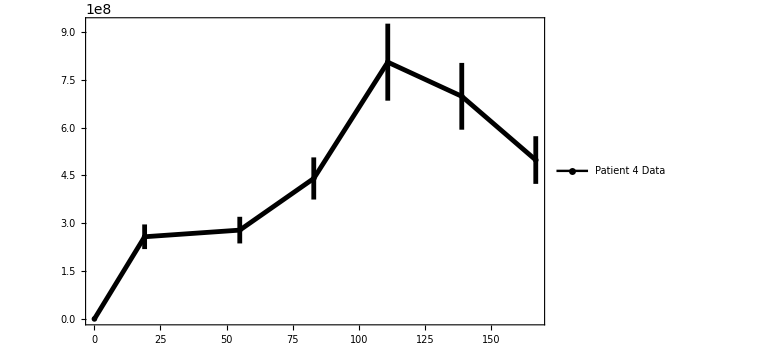

```mathematica
P4Plot=ListLinePlot[patient4adjusteddata,PlotMarkers->{"OpenMarkersThick",8},(*IntervalMarkersStyle->Gray,*)PlotStyle->Directive[Black,Thickness[0.006]],LabelStyle->Directive[Black,Bold, 18],Frame->True,FrameStyle->Directive[Black,Thick],PlotLegends->Placed[LineLegend[{"Patient 4 Data"},legendoptions],{0.2,0.9}],ImageSize->Large](*Patient 4*)
```

```mathematica
patient5adjusteddata=Thread[{patient5[[All,1]],Thread[Around[patient5[[All,3]],Scaled[0.15]]]}]
```

{{0.,1.430.21},{19.,9.31.410^7},{55.,9.01.410^8},{83.,5.60.810^8},{111.,4.80.710^8},{139.,7.21.110^8},{167.,5.80.910^8}}

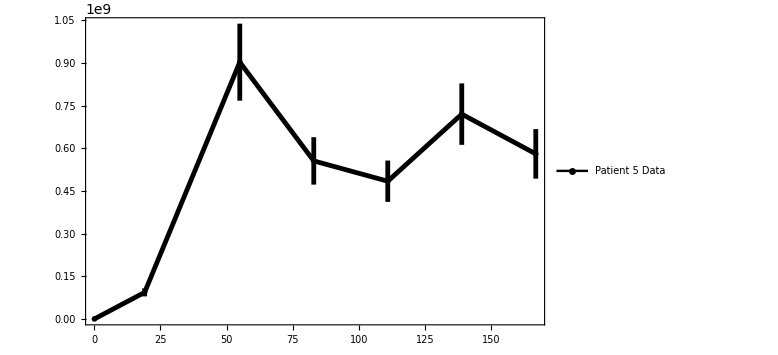

```mathematica
P5Plot=ListLinePlot[patient5adjusteddata,PlotMarkers->{"OpenMarkersThick",8},(*IntervalMarkersStyle->Gray,*)PlotStyle->Directive[Black,Thickness[0.006]],LabelStyle->Directive[Black,Bold, 18],Frame->True,FrameStyle->Directive[Black,Thick],PlotLegends->Placed[LineLegend[{"Patient 5 Data"},legendoptions],{0.75,0.28}],ImageSize->Large]
```

```mathematica
patient6adjusteddata=Thread[{patient6[[All,1]],Thread[Around[patient6[[All,3]],Scaled[0.15]]]}]
```

{{0.,1.430.21},{19.,6.20.910^7},{55.,1.900.2910^8},{83.,1.500.2310^8},{111.,2.060.3110^8},{139.,2.130.3210^8}}

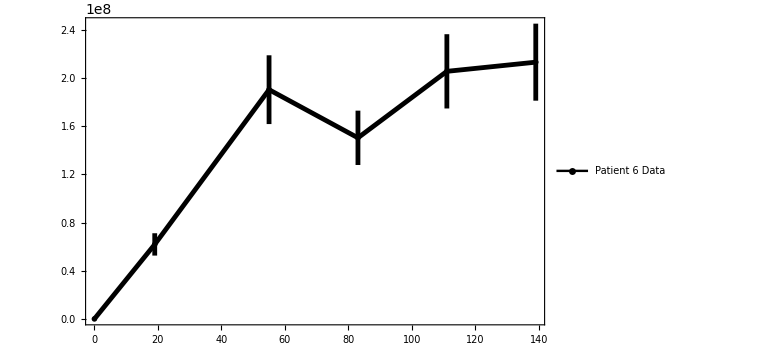

```mathematica
P6Plot=ListLinePlot[patient6adjusteddata,PlotMarkers->{"OpenMarkersThick",8},(*IntervalMarkersStyle->Gray,*)PlotStyle->Directive[Black,Thickness[0.006]],LabelStyle->Directive[Black,Bold, 18],Frame->True,FrameStyle->Directive[Black,Thick],PlotLegends->Placed[LineLegend[{"Patient 6 Data"},legendoptions],{0.2,0.88}],ImageSize->Large]
```

## Solving the non-linear ODE system

```mathematica
DynamicModule[{sol,t,pvax,Ad,Di,Dm,Ncd4,Ncd8,Acd4,Acd8,Ac,Tu,pE,MEj,ME,
pMEj,pME,pMj,pM,Mj,M,pMI,pMII,NA,injectiontimes, Dosea, Dosep,αd,αp,αpE,δM,Ka,Λ,rD,Kdc,Ktc4,Ktc8,Kt,KpM1,KpM2,a,a1,b1,b2,c,c1,c8,d,μ1,μ2,μ3,σNh,σNc,ρ1,ρ2,r,s,λ,kin,kext,kon1,kon2,koff,koffj,VE,VDC,Vsc,βM,βpM,βp,Fp1,Fp2,Vax,AffinbyPatientI,AffinbyPatientII,patientHLAAffinI ,patientHLAAffinII,KDsI,KDsII,KDeffI,KDeffII,p0,Ad0,Di0,Dm0,Ncd40,Ncd80,Acd0,Acd40,Acd80,T0,pE0,ME0,MEj0,jend,kend, n,peptide,adjuv,DCi,DCm,Ncd4p,Ncd8p,Acd4p,Acd8p,tumor,EndoPep,MEjp,MEkp,pMEjp,pMEkp,pMjp,pMkp,Mjp,Mkp,P,v},Manipulate[

P=patient;
v=vaccine;
c=co;c1=c1o;
d=d1o;λ=λo;


If[patient==1,{c=ParmEstim[[1,patient+1]],c1=ParmEstim[[2,patient+1]],d=ParmEstim[[3,patient+1]],λ=ParmEstim[[4,patient+1]]}];

If[patient==2,{c=ParmEstim[[1,patient+1]],c1=ParmEstim[[2,patient+1]],d=ParmEstim[[3,patient+1]],λ=ParmEstim[[4,patient+1]]}];

If[patient==3,{c=ParmEstim[[1,patient+1]],c1=ParmEstim[[2,patient+1]],d=ParmEstim[[3,patient+1]],λ=ParmEstim[[4,patient+1]]}];

If[patient==4,{c=ParmEstim[[1,patient+1]],c1=ParmEstim[[2,patient+1]],d=ParmEstim[[3,patient+1]],λ=ParmEstim[[4,patient+1]]}];

If[patient==5,{c=ParmEstim[[1,patient+1]],c1=ParmEstim[[2,patient+1]],d=ParmEstim[[3,patient+1]],λ=ParmEstim[[4,patient+1]]}];

If[patient==6,{c=ParmEstim[[1,patient+1]],c1=ParmEstim[[2,patient+1]],d=ParmEstim[[3,patient+1]],λ=ParmEstim[[4,patient+1]]}];


injectiontimes = {0,3,7,14,21,83,139}; 
NA=6.0221367*^23; (*Avogadro's constant*)
Dosea=0.5*^3; (*adjuvant concentration per vaccine in mg/L*)
Dosep= {119340,120030,109570,116570,110860,111820};  (*peptide dose in pmols; Used https://www.bioinformatics.org/sms/prot_mw.html to calculate Protein Molecular weight; To convert from weight to moles: http://molbiol.edu.ru/eng/scripts/01_04.html*)
αp=0.28;αd=.5;αpE=70;Fp1={0.006,0.001,0.001,0.001,0.003,0.001};Fp2={0.007,0.002,0.006,0.002,0.002,0.001};a=5.*^7;a1=1.*^3;c8=6.5*^-11;s=0.0839;(*c1=0.835;*)

Λ=3.75;(*0.363;*)
δM=.33;(*Immature (.09) and mature DC death rate*)
rD=2.48;(*1.12;*) (*max maturation rate - DCs (see DC maturation section below-fitted)*)
Ka=6.64;(*4;*) (*mg/L - adjuvant concentration at which immature Dc activation rate is 50% max; value from fitting (see DC maturation section below) *)
Kdc=2.38*^7;  (*DC Carrying capacity; Unit: # cells *)

b1=0.15;b2=0.12;
ρ1=0.0265;ρ2=0.0509;
Ktc4= (8.57*^11)*0.7;  (*T-Cells Carrying capacity; Unit: # cells*)
Ktc8=(8.57*^11)*0.3;  (*CD8 T-Cells Carrying capacity; Unit: # cells *)
μ1=0.031;μ2=0.022;
μ3=0.0029;
σNc=3;σNh=1.5;
KpM1=400;KpM2=400;

Kt=1.45*^10; (*Tumor Carrying capacity Unit: # cells *)
r=0.004;

βp=14.4;
βM=1.663;
βpM=.1663;
VDC=2.5388*^-12; (*https://link.springer.com/article/10.1007/s10928-013-9328-y/tables/2*)
Vsc=4*0.1919;(*;2.75;*)
VE=1*^-14;

(*Input data*)
Vax={3;;15,16;;32,33;;46,47;;60,61;;80,81;;100}; (*6 vaccines, selecting columns that correspond to each vaccine*)
AffinbyPatientI = Select[dataNetMHCIpanAll,#[[1]]==P&]; (*set of HLA's by patient - these are in rows *)
AffinbyPatientII=Select[dataNetMHCIIpanAll,#[[1]]==P&];

(*MHC I molecules*)
KDsI=AffinbyPatientI[[1;;,Vax[[v]]]];(* Calculate KDs for each vaccine and each HLA allotype specific to the patient*)
KDeffI=1/Total[1/Transpose[KDsI]]*1.*^3;(*pmol*)
kon1=1.8144*^-2;
koffj=kon1*KDeffI;

(*MHC II molecules*)
KDsII=AffinbyPatientII[[1;;,Vax[[v]]]];  (* Calculate KDs for each column representing an HLA allotype specific to the patient*)
KDeffII=1/Total[1/Transpose[KDsII]]*1.*^3; (*pmol*) (*list of KDeffs*)
kon2=8.64*^-3;
koff=kon2*KDeffII; (*list of kOFFs*)

(*MHC I & II molecules*)
kin=14.4;
kext=28.8;
jend=Length[AffinbyPatientI]; (*Define total number of j and k alleles for each patient; j is for alleles in MHC-I and k for alleles in MHC-II*)
kend=Length[AffinbyPatientII]; 
n=jend+kend;

(*INITIAL CONDITIONS*)
p0=0;
Ad0=0;
Di0=1*^7;
Dm0=0;
Ncd40=(5.38*^9)*.7;
Ncd80=(5.38*^9)*.3;
Acd0={patient1[[1,3]],patient2[[1,3]],patient3[[1,3]],patient4[[1,3]],patient5[[1,3]],patient6[[1,3]]};
T0={T[τ]/.tumorFun[[1]]/.τ->120,T[τ]/.tumorFun[[2]]/.τ->120,T[τ]/.tumorFun[[3]]/.τ->165,T[τ]/.tumorFun[[4]]/.τ->180,T[τ]/.tumorFun[[5]]/.τ->135,T[τ]/.tumorFun[[6]]/.τ->105};
pE0=0;
MEj0={40*^4/2,40*^4/2,20*^4/2,70*^4/2}/NA*1*^12;
ME0={20*^4/2,20*^4/2,10*^4/2,10*^4/2}/NA*1*^12;

pMI = NA* 1*^-12 Sum[pMj[j][t],{j,jend}];
pMII =NA *1*^-12Sum[pM[k][t],{k,kend}];

sol=NDSolve[Flatten[{
pvax'[t]==-αp pvax[t], (*Peptides in a Vaccine*)
Ad'[t]==-αd Ad[t], (*Adjuvant in a Vaccine*)
Di'[t]== Λ Di[t](1-Di[t]/Kdc)-rD(Ad[t]/(Ka+Ad[t]))Di[t],(*Immature DC*)
Dm'[t]==rD(Ad[t]/(Ka+Ad[t]))Di[t] -δM Dm[t],(*Mature Dc*)
Ncd4'[t]==b1 Ncd4[t](1-Ncd4[t]/Ktc4)-μ3 Ncd4[t]-σNh Ncd4[t]Fp1[[P]](Dm[t]/(Dm[t]+Fp1[[P]]Ncd4[t]+Acd4[t]))(pMII/(pMII+KpM2)),(*Naive CD4*)
Acd4'[t]==c1 (Tu[t]/(a1+Tu[t])) Acd4[t]+σNh Ncd4[t]Fp1[[P]](Dm[t]/(Dm[t]+Fp1[[P]] Ncd4[t]+Acd4[t]))(pMII/(pMII+KpM2))+ρ1 (Dm[t]/(Dm[t]+Fp1[[P]] Ncd4[t]+Acd4[t]))((pMII-KpM2)/(pMII+KpM2))  Acd4[t]-μ1 Acd4[t],(*Active CD4*)

Ncd8'[t]==b2 Ncd8[t](1-Ncd8[t]/Ktc8)-μ3 Ncd8[t]-σNc Ncd8[t]Fp2[[P]](Dm[t]/(Dm[t]+Fp2[[P]] Ncd8[t]+Acd8[t]))(pMI/(pMI+KpM1)),(*Naive CD8*)
Acd8'[t]==c(((d(Acd8[t]/Tu[t])^λ/(s +(Acd8[t]/Tu[t])^λ))^2 Tu[t]^2)/(a+(d(Acd8[t]/Tu[t])^λ/(s +(Acd8[t]/Tu[t])^λ))^2 Tu[t]^2)) Acd8[t]+c8 Acd4[t]Tu[t]+σNc Ncd8[t]Fp2[[P]](Dm[t]/(Dm[t]+Fp2[[P]] Ncd8[t]+Acd8[t]))*(pMI/(pMI+KpM1))+ρ2(Dm[t]/(Dm[t]+Fp2[[P]] Ncd8[t]+Acd8[t]))((pMI-KpM1)/(pMI+KpM1))  Acd8[t]-μ2 Acd8[t],(*Active CD8*)
Ac'[t]== Acd4'[t]+Acd8'[t],
Tu'[t]==r(1-Tu[t]/Kt)Tu[t]-(d(Acd8[t]/Tu[t])^λ/(s +(Acd8[t]/Tu[t])^λ))Tu[t] ,(*Tumor cells*)
(* neo-peptides *)
pE'[t]==αpE pvax[t] VE/Vsc-βp pE[t]-pE[t] (Sum[ kon1/VE MEj[j][t],{j,jend}]+Sum[kon2/VE ME[k][t],{k,kend}])+Sum[koffj [[j]]*pMEj[j][t],{j,jend}]+Sum[koff[[k]]* pME[k][t],{k,kend}],
(* MHCI and MHCII molecules in endosome *)
Table[MEj[j]'[t]==βM(MEj0[[j]]-MEj[j][t])-kon1/VE pE[t]MEj[j][t]+koffj[[j]]* pMEj[j][t]+kin Mj[j][t],{j,jend}],
Table[ME[k]'[t]==βM(ME0[[k]]-ME[k][t])-kon2/VE  pE[t] ME[k][t]+koff[[k]]* pME[k][t]+kin M[k][t],{k,kend}],
(* p-MHCI and p-MHCII complex in endosome *)
Table[pMEj[j]'[t]==kon1/VE pE[t]MEj[j][t]-(koffj[[j]]+βpM+kext)pMEj[j][t],{j,jend}],
Table[pME[k]'[t]==kon2/VE  pE[t]ME[k][t]-(koff[[k]]+βpM+kext)pME[k][t],{k,kend}],
(* p-MHCI and p-MHCII complex in DC membrane *)
Table[pMj[j]'[t]== kext pMEj[j][t]-koffj[[j]]*pMj[j][t],{j,jend}],
Table[pM[k]'[t]== kext pME[k][t]-koff[[k]]*pM[k][t],{k,kend}],
(*Free MHC I and MHC II (j, k) *)
Table[Mj[j]'[t]==koffj [[j]]*pMj[j][t]-kin Mj[j][t],{j,jend}],
Table[M[k]'[t]== koff[[k]]* pM[k][t]-kin M[k][t],{k,kend}],
Flatten[{
pvax[0]==Dosep[[P]],
Ad[0]==Dosea,
Di[0]==Di0,
Dm[0]==Dm0, 
Ncd4[0]==Ncd40,
Ncd8[0]==Ncd80,
Acd4[0]==.7*Acd0[[P]],
Acd8[0]==.3*Acd0[[P]],
Ac[0]==Acd0[[P]],
(*Tu[0]==T0,*)
Tu[0]==T0[[P]],
pE[0]==pE0,
Table[MEj[j][0]==MEj0[[j]],{j,jend}],
Table[ME[k][0]==ME0[[k]],{k,kend}],
Table[pMEj[j][0]==0,{j,jend}],
Table[pME[k][0]==0,{k,kend}],
Table[pMj[j][0]==0,{j,jend}],
Table[pM[k][0]==0,{k,kend}],
Table[Mj[j][0]==0,{j,jend}],
Table[M[k][0]==0,{k,kend}]
}], 
WhenEvent[{t==3,t==7,t==14,t==21,t==83,t==139},{pvax[t]->pvax[t]+ Dosep[[P]],Ad[t]->Ad[t]+Dosea}]
}],
Flatten[{pvax,Ad,Di,Dm,Ncd4,Ncd8,Acd4,Acd8,Ac,Tu,pE,Table[MEj[j],{j,jend}],Table[ME[k],{k,kend}],
Table[pMEj[j],{j,jend}],Table[pME[k],{k,kend}],Table[pMj[j],{j,jend}],Table[pM[k],{k,kend}],Table[Mj[j],{j,jend}],Table[M[k],{k,kend}]}],
{t,0,300},Method->StiffnessSwitching,MaxSteps->50000];

Off[InterpolatingFunction::dmval];

Grid@{{Show[
Plot[{Ac[t]}/.sol,{t,0,200},PlotRange->All, PlotStyle->{Directive[Hue[0.61,1,1],Thickness[0.006]]},PlotLegends->Placed[LineLegend[{" Model Simulation"},legendoptions,Spacings->{0.2,-.5}],{.22,.8}],Frame->True,FrameLabel->{"Time (Days)","Total Activated T Cell Count"},LabelStyle->Directive[Black,Bold, 18],FrameStyle->Directive[Black, Thick],ImageSize->Large],
Which[patient==1,P1Plot,patient==2,P2Plot,patient==3,P3Plot,patient==4,P4Plot,patient==5,P5Plot,patient==6,P6Plot]],
LogPlot[Tu[t]/.sol,{t,0,210},PlotRange->{10^-9,1.0*^12},PlotStyle->Directive[Hue[0.69,.6,1],Thickness[0.005]],Frame->True,Background->None,PlotLegends->Placed[LineLegend[{" Model Simulation"},legendoptions],{.22,.8}],LabelStyle->Directive[Black,Bold, 18],FrameLabel->{"Time (Days)","Tumor Cell Count"},FrameStyle->Directive[Black,Thick],ImageSize->Large]
}},
Row@{
Control[{{patient,1,Style[" Select Patient ID: ",Bold,14]},{1->" P1 ", 2->" P2 ", 3->" P3 ", 4->" P4 ", 5->" P5 ", 6->" P6 "},ControlType->PopupMenu[0,Opener[True,Appearance->Small]]} ],Spacer@30,
Control[{{vaccine,1,Style[" Vaccine ID: ", Bold, 14]},{1->" V1 ", 2->" V2 ", 3->" V3 ", 4->" V4 ", 5->" V5 ", 6->" V6 "},Setter}]},
SynchronousUpdating->False,TrackedSymbols->True]]
```

## Tumor burden model predictions by patient given initial tumor burden

```mathematica
Clear[VaxModelTumor2];
VaxModelTumor2[P_?NumericQ,Tt_?NumericQ,T0var_?NumericQ]:= (VaxModelTumor2[P,Tt,T0var]=Module[{sol,t,pvax,Ad,Di,Dm,Ncd4,Ncd8,Acd4,Acd8,Ac,Tu,pE,MEj,ME,
pMEj,pME,pMj,pM,Mj,M,pMI,pMII,NA,injectiontimes, Dosea, Dosep,αd,αp,αpE,δM,Ka,Λ,rD,Kdc,Ktc4,Ktc8,Kt,KpM1,KpM2,a,a1,b1,b2,c,c1,c2,d,μ1,μ2,μ3,σNh,σNc,ρ1,ρ2,r,s,λ,kin,kext,kon1,kon2,koff,koffj,VE,VDC,Vsc,βM,βpM,βp,Fp1,Fp2,Vax,AffinbyPatientI,AffinbyPatientII,patientHLAAffinI ,patientHLAAffinII,KDsI,KDsII,KDeffI,KDeffII,p0,Ad0,Di0,Dm0,Ncd40,Ncd80,Acd0,Acd40,Acd80,T0,pE0,ME0,MEj0,jend,kend, n,peptide,adjuv,DCi,DCm,Ncd4p,Ncd8p,Acd4p,Acd8p,tumor,EndoPep,MEjp,MEkp,pMEjp,pMEkp,pMjp,pMkp,Mjp,Mkp(*,P*),v},

If[P==1,{v=1,c=ParmEstim[[1,2]],c1=ParmEstim[[2,2]],d=ParmEstim[[3,2]],λ=ParmEstim[[4,2]]}];

If[P==2,{v=2,c=ParmEstim[[1,3]],c1=ParmEstim[[2,3]],d=ParmEstim[[3,3]],λ=ParmEstim[[4,3]]}];

If[P==3,{v=3,c=ParmEstim[[1,4]],c1=ParmEstim[[2,4]],d=ParmEstim[[3,4]],λ=ParmEstim[[4,4]]}];

If[P==4,{v=4,c=ParmEstim[[1,5]],c1=ParmEstim[[2,5]],d=ParmEstim[[3,5]],λ=ParmEstim[[4,5]]}];

If[P==5,{v=5,c=ParmEstim[[1,6]],c1=ParmEstim[[2,6]],d=ParmEstim[[3,6]],λ=ParmEstim[[4,6]]}];

If[P==6,{v=6,c=ParmEstim[[1,7]],c1=ParmEstim[[2,7]],d=ParmEstim[[3,7]],λ=ParmEstim[[4,7]]}];


injectiontimes = {0,3,7,14,21,83,139}; 
NA=6.0221367*^23; (*Avogadro's constant*)
Dosea=0.5*^3; (*adjuvant concentration per vaccine in mg/L*)
Dosep= {119340,120030,109570,116570,110860,111820};  (*peptide dose in pmols; Used https://www.bioinformatics.org/sms/prot_mw.html to calculate Protein Molecular weight; To convert from weight to moles: http://molbiol.edu.ru/eng/scripts/01_04.html*)
αp=0.28;αd=.5;αpE=70;Fp1={0.006,0.001,0.001,0.001,0.003,0.001};Fp2={0.007,0.002,0.006,0.002,0.002,0.001};a=5.*^7;a1=1.*^3;c2=6.5*^-11;s=0.0839;(*c1=0.835;*)

Λ=3.75;(*0.363;*)
δM=.33;(*Immature (.09) and mature DC death rate*)
rD=2.48;(*1.12;*) (*max maturation rate - DCs (see DC maturation section below-fitted)*)
Ka=6.64;(*4;*) (*mg/L - adjuvant concentration at which immature Dc activation rate is 50% max; value from fitting (see DC maturation section below) *)
Kdc=2.38*^7;  (*DC Carrying capacity; Unit: # cells *)

b1=0.15;b2=0.12;ρ1=0.0265;ρ2=0.0509;
Ktc4= (8.57*^11)*0.7;  (*T-Cells Carrying capacity; Unit: # cells*)
Ktc8=(8.57*^11)*0.3;  (*CD8 T-Cells Carrying capacity; Unit: # cells *)
μ1=0.031;μ2=0.022;
μ3=0.0029;
(*ρ1=1.51;ρ2=2.6;*)(*1*^-5;*)
σNc=3;σNh=1.5;
KpM1=400;KpM2=400;

Kt=1.45*^10; (*Tumor Carrying capacity Unit: # cells *)
r=0.004;(*0.006;*)(*d1=4.98*^-7;d2=5.1*^-7;*)
(*d1=0.17;d2= 0.1;λ=3;s1=50;s2=50;*)

βp=14.4;
βM=1.663;
βpM=.1663;
VDC=2.5388*^-12; (*https://link.springer.com/article/10.1007/s10928-013-9328-y/tables/2*)
Vsc=4*0.1919;(*;2.75;*)
VE=1*^-14;

(*Input data*)
Vax={3;;15,16;;32,33;;46,47;;60,61;;80,81;;100}; (*6 vaccines, selecting columns that correspond to each vaccine*)
AffinbyPatientI = Select[dataNetMHCIpanAll,#[[1]]==P&]; (*set of HLA's by patient - these are in rows *)
AffinbyPatientII=Select[dataNetMHCIIpanAll,#[[1]]==P&];

(*MHC I molecules*)
	   KDsI=AffinbyPatientI[[1;;,Vax[[v]]]];(* Calculate KDs for each vaccine and each HLA allotype specific to the patient*)
KDeffI=1/Total[1/Transpose[KDsI]]*1.*^3;(*pmol*)
kon1=1.8144*^-2;
koffj=kon1*KDeffI;

(*MHC II molecules*)
KDsII=AffinbyPatientII[[1;;,Vax[[v]]]];  (* Calculate KDs for each column representing an HLA allotype specific to the patient*)
KDeffII=1/Total[1/Transpose[KDsII]]*1.*^3; (*pmol*) (*list of KDeffs*)
kon2=8.64*^-3;
koff=kon2*KDeffII; (*list of kOFFs*)

(*MHC I & II molecules*)
kin=14.4;
kext=28.8;
jend=Length[AffinbyPatientI]; (*Define total number of j and k alleles for each patient; j is for alleles in MHC-I and k for alleles in MHC-II*)
kend=Length[AffinbyPatientII]; 
n=jend+kend;

(*INITIAL CONDITIONS*)
p0=0;
Ad0=0;
Di0=1*^7;
Dm0=0;
Ncd40=(5.38*^9)*.7;
Ncd80=(5.38*^9)*.3;
Acd0={patient1[[1,3]],patient2[[1,3]],patient3[[1,3]],patient4[[1,3]],patient5[[1,3]],patient6[[1,3]]};
T0=T0var;
(*T0={T[τ]/.tumorFun[[1]]/.τ->120,T[τ]/.tumorFun[[2]]/.τ->120,T[τ]/.tumorFun[[3]]/.τ->165,T[τ]/.tumorFun[[4]]/.τ->180,T[τ]/.tumorFun[[5]]/.τ->135,T[τ]/.tumorFun[[6]]/.τ->105};*)
pE0=0;
MEj0={40*^4/2,40*^4/2,20*^4/2,70*^4/2}/NA*1*^12;
ME0={20*^4/2,20*^4/2,10*^4/2,10*^4/2}/NA*1*^12;

pMI = NA* 1*^-12 Sum[pMj[j][t],{j,jend}];
pMII =NA *1*^-12Sum[pM[k][t],{k,kend}];

sol=NDSolve[Flatten[{
pvax'[t]==-αp pvax[t], (*Peptides in a Vaccine*)
Ad'[t]==-αd Ad[t], (*Adjuvant in a Vaccine*)
Di'[t]== Λ Di[t](1-Di[t]/Kdc)-rD(Ad[t]/(Ka+Ad[t]))Di[t],(*Immature DC*)
Dm'[t]==rD(Ad[t]/(Ka+Ad[t]))Di[t] -δM Dm[t],(*Mature Dc*)
Ncd4'[t]==b1 Ncd4[t](1-Ncd4[t]/Ktc4)-μ3 Ncd4[t]-σNh Ncd4[t]Fp1[[P]](Dm[t]/(Dm[t]+Fp1[[P]]Ncd4[t]+Acd4[t]))(pMII/(pMII+KpM2)),(*Naive CD4*)
Acd4'[t]==c1 (Tu[t]/(a1+Tu[t])) Acd4[t]+σNh Ncd4[t]Fp1[[P]](Dm[t]/(Dm[t]+Fp1[[P]] Ncd4[t]+Acd4[t]))(pMII/(pMII+KpM2))+ρ1 (Dm[t]/(Dm[t]+Fp1[[P]] Ncd4[t]+Acd4[t]))((pMII-KpM2)/(pMII+KpM2))  Acd4[t]-μ1 Acd4[t],(*Active CD4*)

Ncd8'[t]==b2 Ncd8[t](1-Ncd8[t]/Ktc8)-μ3 Ncd8[t]-σNc Ncd8[t]Fp2[[P]](Dm[t]/(Dm[t]+Fp2[[P]] Ncd8[t]+Acd8[t]))(pMI/(pMI+KpM1)),(*Naive CD8*)
Acd8'[t]==c(((d(Acd8[t]/Tu[t])^λ/(s +(Acd8[t]/Tu[t])^λ))^2 Tu[t]^2)/(a+(d(Acd8[t]/Tu[t])^λ/(s +(Acd8[t]/Tu[t])^λ))^2 Tu[t]^2)) Acd8[t]+c2 Acd4[t]Tu[t]+σNc Ncd8[t]Fp2[[P]](Dm[t]/(Dm[t]+Fp2[[P]] Ncd8[t]+Acd8[t]))*(pMI/(pMI+KpM1))+ρ2(Dm[t]/(Dm[t]+Fp2[[P]] Ncd8[t]+Acd8[t]))((pMI-KpM1)/(pMI+KpM1))  Acd8[t]-μ2 Acd8[t],(*Active CD8*)
Ac'[t]== Acd4'[t]+Acd8'[t],
Tu'[t]==r(1-Tu[t]/Kt)Tu[t]-(d(Acd8[t]/Tu[t])^λ/(s +(Acd8[t]/Tu[t])^λ))Tu[t] ,(*Tumor cells*)
(* neo-peptides *)
pE'[t]==αpE pvax[t] VE/Vsc-βp pE[t]-pE[t] (Sum[ kon1/VE MEj[j][t],{j,jend}]+Sum[kon2/VE ME[k][t],{k,kend}])+Sum[koffj [[j]]*pMEj[j][t],{j,jend}]+Sum[koff[[k]]* pME[k][t],{k,kend}],
(* MHCI and MHCII molecules in endosome *)
Table[MEj[j]'[t]==βM(MEj0[[j]]-MEj[j][t])-kon1/VE pE[t]MEj[j][t]+koffj[[j]]* pMEj[j][t]+kin Mj[j][t],{j,jend}],
Table[ME[k]'[t]==βM(ME0[[k]]-ME[k][t])-kon2/VE  pE[t] ME[k][t]+koff[[k]]* pME[k][t]+kin M[k][t],{k,kend}],
(* p-MHCI and p-MHCII complex in endosome *)
Table[pMEj[j]'[t]==kon1/VE pE[t]MEj[j][t]-(koffj[[j]]+βpM+kext)pMEj[j][t],{j,jend}],
Table[pME[k]'[t]==kon2/VE  pE[t]ME[k][t]-(koff[[k]]+βpM+kext)pME[k][t],{k,kend}],
(* p-MHCI and p-MHCII complex in DC membrane *)
Table[pMj[j]'[t]== kext pMEj[j][t]-koffj[[j]]*pMj[j][t],{j,jend}],
Table[pM[k]'[t]== kext pME[k][t]-koff[[k]]*pM[k][t],{k,kend}],
(*Free MHC I and MHC II (j, k) *)
Table[Mj[j]'[t]==koffj [[j]]*pMj[j][t]-kin Mj[j][t],{j,jend}],
Table[M[k]'[t]== koff[[k]]* pM[k][t]-kin M[k][t],{k,kend}],
Flatten[{
pvax[0]==Dosep[[P]],
Ad[0]==Dosea,
Di[0]==Di0,
Dm[0]==Dm0, 
Ncd4[0]==Ncd40,
Ncd8[0]==Ncd80,
Acd4[0]==.7*Acd0[[P]],
Acd8[0]==.3*Acd0[[P]],
Ac[0]==Acd0[[P]],
Tu[0]==T0,
pE[0]==pE0,
Table[MEj[j][0]==MEj0[[j]],{j,jend}],
Table[ME[k][0]==ME0[[k]],{k,kend}],
Table[pMEj[j][0]==0,{j,jend}],
Table[pME[k][0]==0,{k,kend}],
Table[pMj[j][0]==0,{j,jend}],
Table[pM[k][0]==0,{k,kend}],
Table[Mj[j][0]==0,{j,jend}],
Table[M[k][0]==0,{k,kend}]
}], 
WhenEvent[{t==3,t==7,t==14,t==21,t==83,t==139},{pvax[t]->pvax[t]+ Dosep[[P]],Ad[t]->Ad[t]+Dosea}]
}],
Flatten[{pvax,Ad,Di,Dm,Ncd4,Ncd8,Acd4,Acd8,Ac,Tu,pE,Table[MEj[j],{j,jend}],Table[ME[k],{k,kend}],
Table[pMEj[j],{j,jend}],Table[pME[k],{k,kend}],Table[pMj[j],{j,jend}],Table[pM[k],{k,kend}],Table[Mj[j],{j,jend}],Table[M[k],{k,kend}]}],
{t,0,300},Method->StiffnessSwitching,MaxSteps->50000];
Flatten[{Tu[Tt]/.sol}]
])
```

```mathematica
stages = {"≤2.4 mm","≤6.4 mm","≤23.5 mm","≤80.2 mm"};
```

```mathematica
T0=LHCSampling[30000,0,2.*^10,0.02,"unif",2000];
```

```mathematica
InitT02fin0={};
For[i=1,i≤Length[T0],i++,
For[j=1,j≤6,j++,InitT02fin=Flatten[{j,Quiet[Check[VaxModelTumor2[j,200,T0[[i]]],Continue[],{Power::infy,NDSolve::ndnum,NDSolve::ndsz,NDSolve::mxst}]],T0[[i]],Which[T0[[i]]≤500000,Replace[T0[[i]],T0[[i]]->stages[[1]]],500000<T0[[i]]≤1*^7,Replace[T0[[i]],T0[[i]]->stages[[2]]],1*^7<T0[[i]]≤5*^8,Replace[T0[[i]],T0[[i]]->stages[[3]]],5*^8<T0[[i]],Replace[T0[[i]],T0[[i]]->stages[[4]]]]}];
AppendTo[InitT02fin0,InitT02fin]]
]//AbsoluteTiming
```

```mathematica
tumorICSPs=InitT02fin0;
```

```mathematica
Export["tumorICS_AllPatients.dat",tumorICSPs];
```

```mathematica
Clear[InitT02fin0]
```

```mathematica
tumorICSPs
```

{{1,135840.,1.60081×10^10,≤80.2 mm},{2,1.50346×10^9,1.60081×10^10,≤80.2 mm},{3,276445.,1.60081×10^10,≤80.2 mm},{4,373773.,1.60081×10^10,≤80.2 mm},11425,{3,270328.,1.55889×10^10,≤80.2 mm},{4,364721.,1.55889×10^10,≤80.2 mm},{5,1.9718×10^6,1.55889×10^10,≤80.2 mm},{6,4.72378×10^7,1.55889×10^10,≤80.2 mm}}
 |  |  |  |

```mathematica
Export["tumorICS_AllPatients.csv",InitT02fin0 ,"CSV"];
```

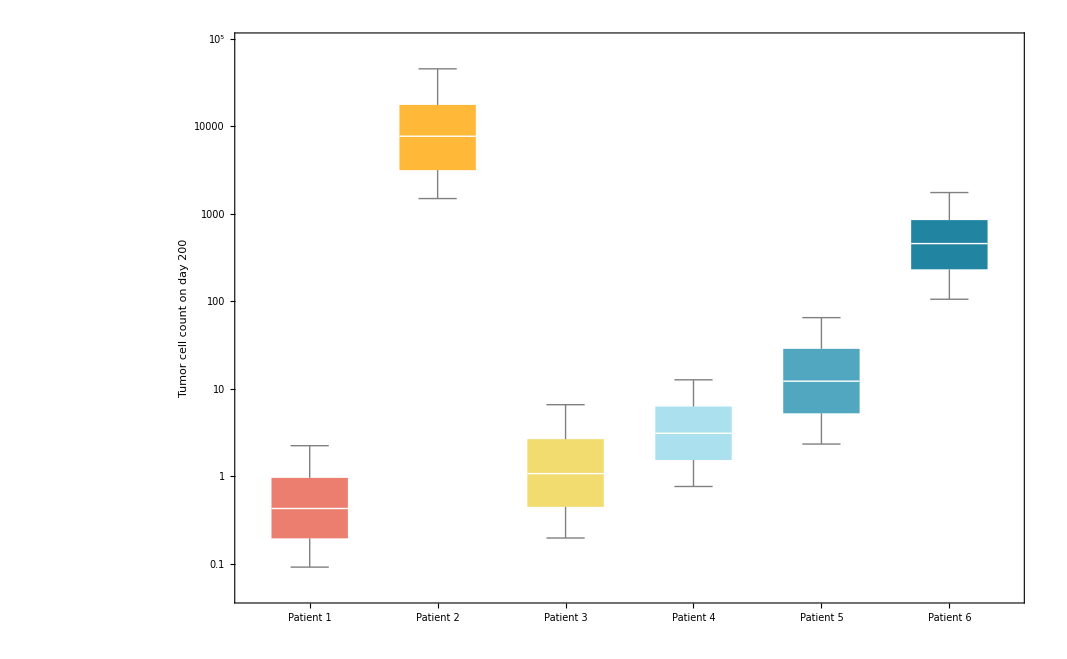
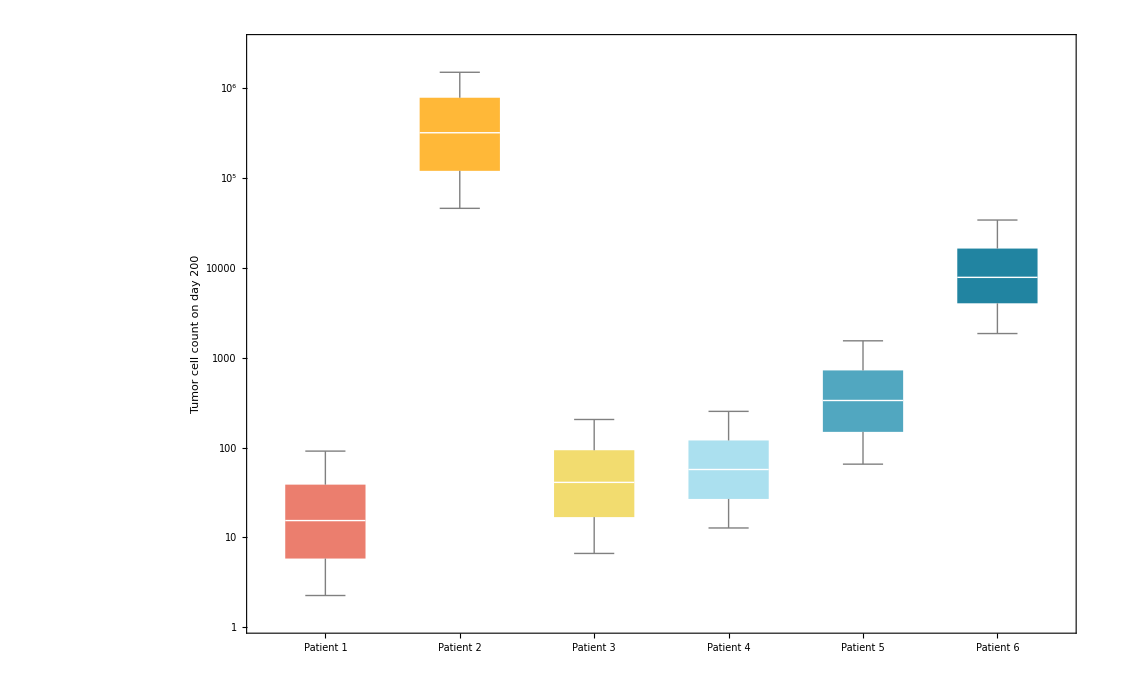
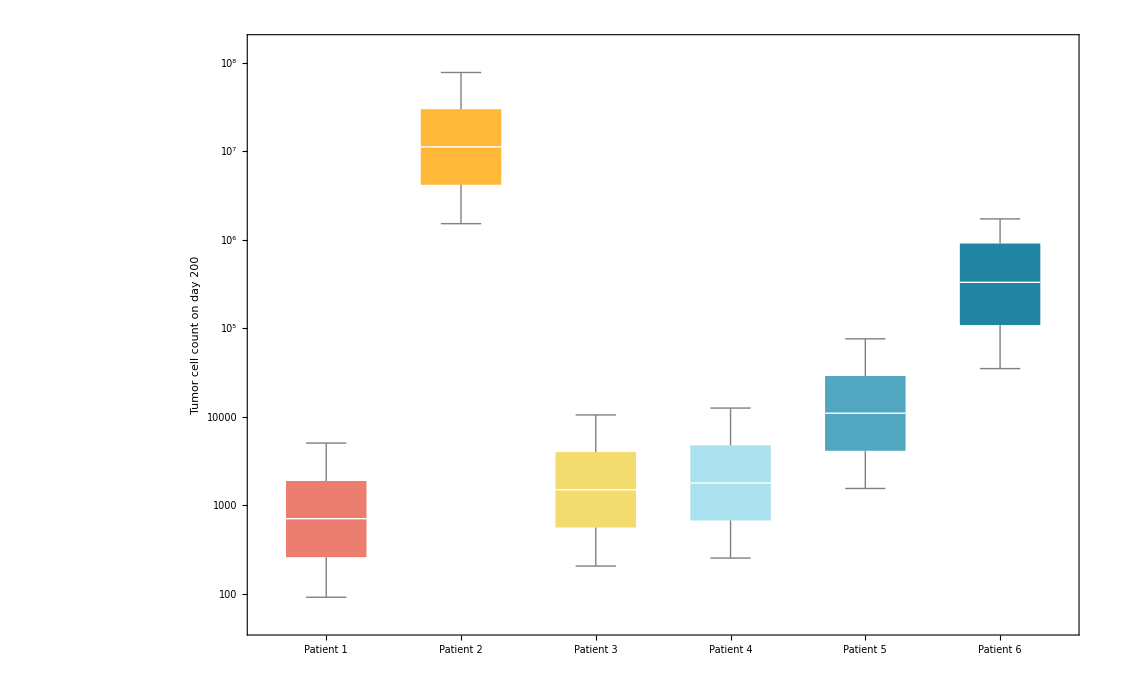
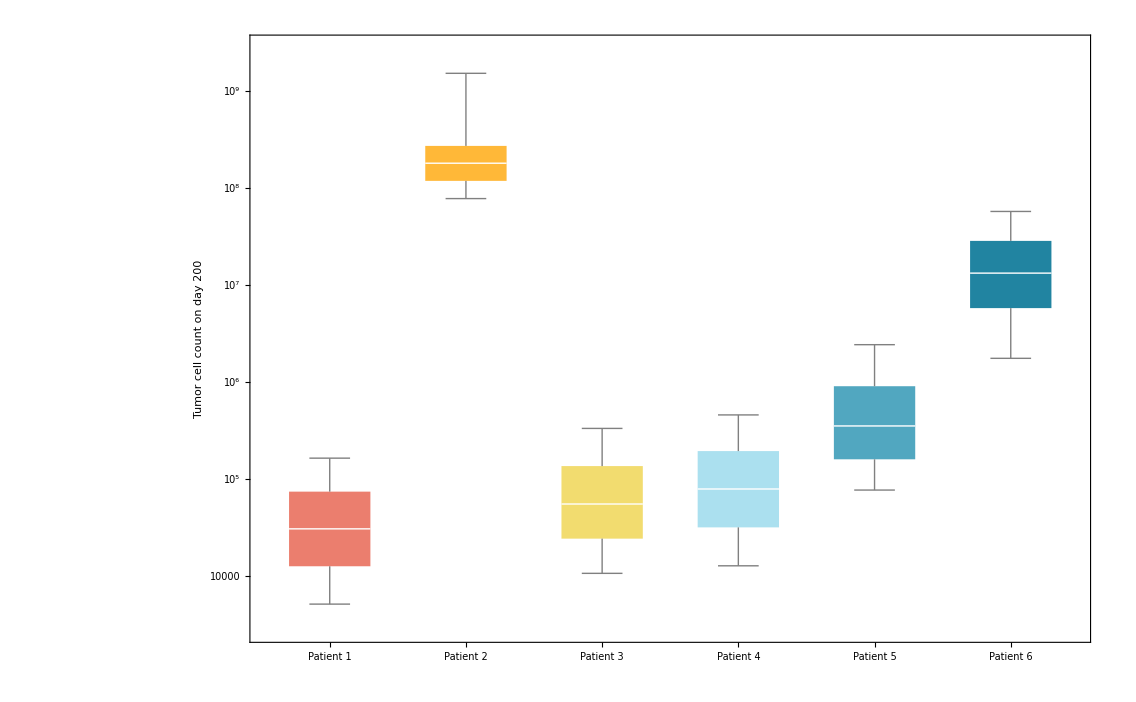

```mathematica
Table[BoxWhiskerChart[#[[All,All,2]],ScalingFunctions->"Log",(*ChartLabels->#[[All,1,1]],*)ChartLabels->{"Patient 1","Patient 2","Patient 3","Patient 4","Patient 5","Patient 6"},FrameLabel->{{"Tumor cell count on day 200",None},{None,"Initial tumor diameter size:"stages[[i]]}},FrameTicks->{{All,{{50000,"≤1 mm"},{500000,"≤2.4 mm"},{1*^7,"≤6.4 mm" },{5*^8,"≤23.4 mm"},{1*^10,"≤80.2 mm"}}},{None,All}},ChartBaseStyle->{Thick}, ChartStyle->24,GridLines->{None,{{Log[50000],Dashed},{Log[500000],Dashed},{Log[1*^7],Dashed},{Log[5*^8],Dashed},{Log[1*^10],Dashed}}},GridLinesStyle->Directive[Black, Thick],LabelStyle->Directive[Black,Bold, 25],FrameStyle->Directive[Black],ImageSize->Large]&[ GatherBy[Select[tumorICSPs,#[[4]]==stages[[i]]&],#[[1]]&]],{i,Length[stages]}]
```